```mathematica
(* Sets the Base directory, changing which files are easiest to acces. *)
dropBoxOn=FileNameJoin[{"Dropbox","00School","research"}];
labComp=FileNameJoin[{"C:","Users","karl",dropBoxOn}];(* Lab computer is Windows, so needs "C:" at beginning"  *)
homeComp=FileNameJoin[{"/","home","karl",dropBoxOn}]; (* Home coputer is Linux, so needs "/" at beginning *)
(* The folder that contains the different data runs to analyze, this folder contains subfolders with 
individual runs.*)
dataFolder=FileNameJoin[{homeComp}]
SetDirectory[dataFolder];
(* Make a list of directories to easily select the folder you would like to work with.*)
directories=Select[FileNames["*","",1],DirectoryQ];
For[i=1,i<=Length[directories],i++,
Print[i -> directories[[i]]];]
```

/home/karl/Dropbox/00School/research

1→3_15_17_AimingFor5e12

2→4-18-17

3→data

4→Data Before 4-1-17

5→firstRun2017

6→labBook

7→legacy

8→machineShopOrders

9→mathematicaCode

10→operationManuals

11→papers

12→polarization_4-18-17

13→polarization_4-4-17

14→polarization_4-6-17

15→probeLaserPower

16→pumpLaserFindingCircular_3-29_17

17→RbControlPiPrograms

18→rbsim

19→requisitions

20→wavemeterNoRb

21→wavemeterReliability_3-30-17

22→wmReliability_4-7-17

```mathematica
(* set rootFolder to the folder name containing the desired Files *)
rootFolder=FileNameJoin[{dataFolder,directories[[2]],"probeDrift"}];
SetDirectory[rootFolder];
(* Obtain the filenames of the rotation data and print them out.*)
scanFiles=FileNames["FDayScan"~~RegularExpression[".{25,25}"]~~"Analysis.dat"];
For[i=1,i<=Length[scanFiles],i++,
Print[i -> scanFiles[[i]]];]

(*Import the faraday rotation data*)
rotationAnalysisDataFile=Import[FileNameJoin[{rootFolder,scanFiles[[3]]}],"tsv"];
```

1→FDayScan2017-04-18_112432RotationAnalysis.dat

2→FDayScan2017-04-18_112714RotationAnalysis.dat

3→FDayScan2017-04-18_113047RotationAnalysis.dat

4→FDayScan2017-04-18_113347RotationAnalysis.dat

5→FDayScan2017-04-18_113832RotationAnalysis.dat

6→FDayScan2017-04-18_114059RotationAnalysis.dat

7→FDayScan2017-04-18_115623RotationAnalysis.dat

8→FDayScan2017-04-18_115845RotationAnalysis.dat

9→FDayScan2017-04-18_120414RotationAnalysis.dat

10→FDayScan2017-04-18_120647RotationAnalysis.dat

11→FDayScan2017-04-18_143958RotationAnalysis.dat

12→FDayScan2017-04-18_144442RotationAnalysis.dat

13→FDayScan2017-04-18_145357RotationAnalysis.dat

65.3

64.5

0

300

400

500

800

{{31.1691,-76.6144},{28.5359,-76.5778},{26.2112,-79.0828},{23.5545,-76.3896},{20.9452,-76.3919},{18.415,-76.2954},{15.9164,-76.1585},{13.1175,-75.9545},{10.2915,-75.7953},{7.47227,-80.7244}}

200

{{0.641317,-73.5462},{-1.39843,-76.6972},{-3.91251,-74.7549},{-6.14195,-74.8268},{-8.75084,-75.0461},{-11.4546,-74.8169},{-14.4428,-74.7039},{-17.7156,-74.6984},{-21.1781,-74.9687},{-24.5931,-74.9101}}

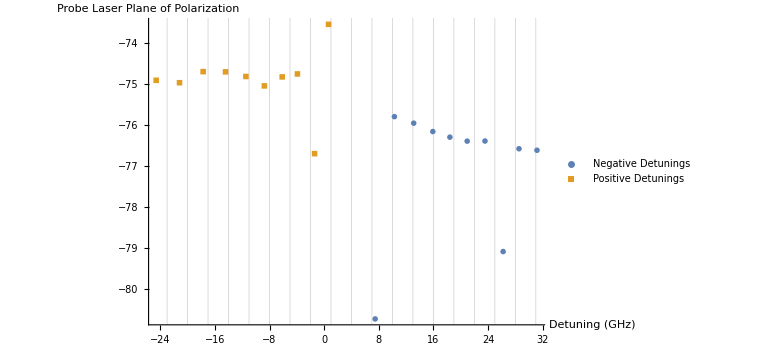

55.7622

7.17818

0.128729

```mathematica
(* Define important constants of data processing *)
fileNumber=9;
rotationAnalysisData=Import[FileNameJoin[{rootFolder,scanFiles[[fileNumber]]}],"tsv"];
rotAnalDataStartRow=16; (* Used to know how many lines to remove so we are just working with data *)
aoutColumn=1;
wavelengthColumn=2;
angleColumn=10;

(* Define important physical constants*)
c=2.99792458*^8;
ν0=377107.463;
(* Retrieves the recorded voltages of the magnets *)
v1=rotationAnalysisData[[11]][[2]]
v2=rotationAnalysisData[[12]][[2]]
(* The coefficients for the polynomial describing the magnetic field of magnet 1 [(c)oefficient of magent (1)]  based on the current.
Assumes x is measured in cm *)
c1x2=.085;
c1x1=-1.907;
c1x0=17.24;
c2x2=0.153;
c2x1=1.866;
c2x0=15.594;

(* The coefficients for the linear relationship between the current and the voltage of the magnets *)
c1v2iSlope=.0504;
c1v2iInt=-.0113;
c2v2iSlope=.0488;
c2v2iInt=-.0069;

(* Calculate the current in each of the magnets based on the voltage *)
i1=v1*c1v2iSlope+c1v2iInt;
i2=v2*c2v2iSlope+c2v2iInt;

(*Creates a function for obtaining the magnetic field at a given position based on the currents
in the magnets *)
getBEq[i1_,i2_]:=((c1x2 )i1 +(c2x2)i2) x^2 +((c1x1 )i1 +(c2x1)i2) x +((c1x0 )i1 +(c2x0)i2)  ;
BdotL=Integrate[getBEq[i1,i2],{x,0,2.794}] /100/10000;(* Divide by 100 to convert to Gauss*meters, Divide by 10000 to convert to Tesla*meters*)

(* I love these things. By creating a function with a module you can create "functions" in the traditional C programming sense, where you have multiple inputs with one output. *)
(* ApproximateFrequency calculates the approximate frequency in the missing gap of the frequency measurements that we collected. *)
ApproximateFrequency[data_,columnMissing_,columnReference_,missingEntry_]:=Module[{j,adjacentSpots,referenceSpacing,validEntries,fit}(*These are your local variables that aren't stored beyond the scope of the module.*),
(*Selects the data that is certainly an appropriate measure of wavelength *)
validEntries=Take[data,All,{1,2}];
validEntries=validEntries[Select[#[[columnMissing]]>7000000&]];
(*The "reference column" is the column that is monotonically increasing, we need to know what the size of spaces between these values is *)
referenceSpacing=Abs[data[[2]][[columnReference]]-data[[1]][[columnReference]]];
j=1;
(* This "While" loop accumulates adjacent data points used to approximate the missing frequency, we only want the closest datapoints. *)
While[And[Length[adjacentSpots]<3,Abs[j*referenceSpacing]<1024](* We want a few data points to approximate where our point lies, keep going until we have at least 3*),
adjacentSpots=validEntries[Select[Abs[#[[columnReference]]-missingEntry]≤referenceSpacing*j&]];
j++;
];
fit=LinearModelFit[Normal[adjacentSpots],x,x];
Print[missingEntry];
fit[missingEntry] (* Last line is the "return" statement, all other lines need a semi-colon*)
];

(* This is called on a dataset to fill in all of the missing frequency gaps.*)
FillInMissedFrequencies[rawdata_,columnMissing_,columnReference_]:=Module[{referenceSpacing,missingEntries,validEntries,adjacentSpots,estimatedFrequency,linearModel,dataCopy,dataReturn,position,approxValue,data2,k},
dataCopy=Dataset[rawdata];
dataReturn=Normal[dataCopy];
missingEntries=dataCopy[Select[#[[columnMissing]]<7000000&]];
missingEntries=Transpose[Normal[missingEntries]][[columnReference]];
For[k=1,k<=Length[missingEntries],k++,
approxValue=ApproximateFrequency[dataCopy,columnMissing,columnReference,missingEntries[[k]]];
(* Find the index of the missing value in the list *)
position=Position[dataCopy,missingEntries[[k]]][[1,1]];
(* Use the index to insert the approximate value in the data  *)
dataReturn[[position,columnMissing]]=approxValue;
];
dataReturn
];

(* This removes the majority of the data that we're not interested in for Faraday rotation purposes*)
StripFaradayData[data_]:=Drop[Take[data,{rotAnalDataStartRow,-1},{aoutColumn,angleColumn}],None,{wavelengthColumn+1,angleColumn-wavelengthColumn+1}];

(* Converts the wavelength value reported as an integer to a detuning (GHz) *)
ConvertFDayWavelengthToDetune[data_]:=Module[{wavelengthInteger,θ,lists,wavelengthnm,wavelength,detuning},
lists=Transpose[data];
wavelengthInteger=lists[[1]];
θ=lists[[2]];
wavelengthnm=wavelengthInteger/10000;
detuning=c/(wavelengthnm)-ν0;
Transpose[{detuning,θ}]
];

rotationAnalysisData=StripFaradayData[rotationAnalysisData];
rotationAnalysisData=FillInMissedFrequencies[rotationAnalysisData,2,1];
rotationAnalysisData=Take[rotationAnalysisData,All,{2,-1}];
negativeDetunings=ConvertFDayWavelengthToDetune[rotationAnalysisData]

rotationAnalysisData=Import[FileNameJoin[{rootFolder,scanFiles[[fileNumber+1]]}],"tsv"];
rotationAnalysisData=StripFaradayData[rotationAnalysisData];
rotationAnalysisData=FillInMissedFrequencies[rotationAnalysisData,2,1];
rotationAnalysisData=Take[rotationAnalysisData,All,{2,-1}];
positiveDetunings=ConvertFDayWavelengthToDetune[rotationAnalysisData]


allDetuningsPlot=ListPlot[{Legended[negativeDetunings,"Negative Detunings"],Legended[positiveDetunings,"Positive Detunings"]},PlotRange->All,LabelStyle->18,PlotMarkers->{Automatic,Large},AxesLabel->{"Detuning (GHz)","Probe Laser\nPlane of Polarization"},ImageSize->Large,GridLines->{Range[-35,35,3],None}]

allDetunings=Join[negativeDetunings,positiveDetunings];
detMinMax={Min[Transpose[allDetunings][[1]]],Max[Transpose[allDetunings][[1]]]};
angleMinMax={Min[Transpose[allDetunings][[2]]],Max[Transpose[allDetunings][[2]]]};
run=detMinMax[[2]]-detMinMax[[1]]
rise=angleMinMax[[2]]-angleMinMax[[1]]
rise/run
```

```mathematica
allDetuningsPlot//Rasterize
```

-Graphics-

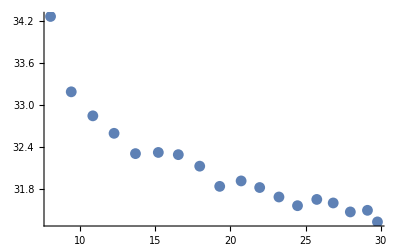

-Graphics-

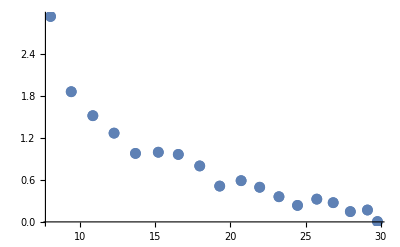

```mathematica
negativeCutoffs={7,35};
positiveCutoffs={7,35};
detuningOffset=0;


model=a/(δ)^2+b/(δ)^4+d;


temp=Dataset[positiveDetunings];
temp=temp[Select[Abs[#[[1]]]<positiveCutoffs[[2]]&]];
temp=temp[Select[Abs[#[[1]]]>positiveCutoffs[[1]]&]];
ListPlot[Normal[temp]]

nlmFit =NonlinearModelFit[Normal[temp],model,{{{a,1},{b,1},{d,0}},δ];
replacements=nlmFit["BestFitParameters"];

temp =Transpose[Normal[temp]];
temp[[2]]=temp[[2]]-d/.replacements;
positiveDetuningsZeroed=Transpose[{temp[[1]]-detuningOffset,temp[[2]]}];


temp=Dataset[positiveDetunings];
temp=temp[Select[Abs[#[[1]]]<negativeCutoffs[[2]]&]];
temp=temp[Select[Abs[#[[1]]]>negativeCutoffs[[1]]&]];
ListPlot[Normal[temp]]
(*
nlmFit =NonlinearModelFit[Normal[temp],model(*,e>-10,e<10}*),{{a,1},{b,1},{d,0}},δ];
replacements=nlmFit["BestFitParameters"];
*)

temp =Transpose[Normal[temp]];
temp[[2]]=temp[[2]]-d/.replacements;
negativeDetuningsZeroed=Transpose[{temp[[1]]-detuningOffset,temp[[2]]}];
allDataZeroed=Join[positiveDetuningsZeroed,negativeDetuningsZeroed];
ListPlot[allDataZeroed]
```

Fit Parameters for Number Density

{a1→311.511,a2→9033.15,θ0→-0.0890432,b→-3.49585}

Parameter Errors 1/δ^2+1/δ^4

FittedModel::constr: The property values {"ParameterErrors"} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

Replacements Excluding δ^4

{a1→276.375,θ0→-0.0758107,b→-1.83775}

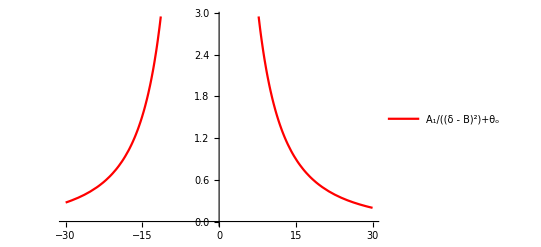

Parameter Errors 1/δ^2

FittedModel::constr: The property values {"ParameterErrors"} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

Number Density (cm^-3):

1.93184×10^14

FittedModel::constr: The property values {"ParameterErrors"} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

General::stop: Further output of FittedModel :: constr will be suppressed during this calculation.

Number Density Error (cm^-3):

2.65093×10^15

Number Density Simple(cm^-3):

1.71394×10^14

-Graphics-

```mathematica
(* Calculates fit for data *)
(* Removes datapoints that wrapped in rotation *)
For[low=5,low<6,low+=5,
lowerBoundDetuning=low;
upperBoundDetuning= 35;
dataset=Dataset[negativeDetuningsZeroed];
dataset=dataset[Select[Abs[#[[1]]]<upperBoundDetuning&]];
dataset=dataset[Select[Abs[#[[1]]]>lowerBoundDetuning&]];
alldata = Normal[dataset];
labelSize=18;

ClearAll[δ,a1,a2,c,θ0,b,nlmFit,replacements];
$Assumptions=a1>0;
$Assumptions=a2>0;
dataset=Dataset[alldata];
min=Dataset[allDataZeroed][Min,2];
max=Dataset[allDataZeroed][Max,2];
maxmin={max,min};
ListPlot[Normal[dataset],PlotRange->All];
νo=377.107;
model=a1/(δ-b)^2+a2/(δ-b)^4+θ0;
Print["Fit Parameters for Number Density"];
nlmFit =NonlinearModelFit[Normal[dataset],{model,a1>0},{{a1,1},{a2,1},{θ0,0},{b,1}},δ];
replacements=nlmFit["BestFitParameters"];
Print[replacements];
plot=Plot[Legended[Evaluate[model/.replacements],"A_1/(δ - B)^2+A_2/(δ - B)^4+θ_o"],{δ,30,-30},PlotRange->{Min[maxmin]-.01,Max[maxmin]+.01},PlotStyle->color,LabelStyle->labelSize];
Print["Parameter Errors 1/δ^2+1/δ^4"];
errors=nlmFit["ParameterErrors"];
{δl,θl}=Transpose[Normal[dataset]];


modelNo4=a1/(δ-b)^2+θ0;
Print["Replacements Excluding δ^4"];
nlmFit2=NonlinearModelFit[Normal[dataset],{modelNo4,a1>0},{{a1,4},{θ0,0},{b,1}},δ,AccuracyGoal->5];
replacementsNo4=nlmFit2["BestFitParameters"];
Print[replacementsNo4];
plotNo4=Plot[Legended[Evaluate[modelNo4/.replacementsNo4],"A_1/(δ - B)^2+θ_o"],{δ,30,-30},PlotRange->{Min[maxmin]-.01,Max[maxmin]+.01},PlotStyle->Red,LabelStyle->labelSize];
Print[plotNo4];
modelfNo4=Function[{δ},Evaluate[modelNo4/.replacementsNo4]];
{δl,θl}=Transpose[Normal[dataset]];
Print["Parameter Errors 1/δ^2"];
errorsNo4=nlmFit2["ParameterErrors"];

linearRotationFit=LinearModelFit[Normal[dataset],x,x];

c=2.99792458*^8;
re=2.8179*^-15;
fge=0.34231;
k=4/3;
BdotL;
μ=9.2740*^-24;
h=6.6261*^-34;
ν0=377107.463;
conversionFactor=h/(BdotL*c*re*fge*k*μ)*10^18*10^-6;(*Conversion Factor is in 1/(Hz)^2, so we need *10^18 to convert to 1/(GHz)^2*)

Print["Number Density (cm^-3):"];
n=(a1/.replacements)* conversionFactor;
Print[n];
errors=nlmFit["ParameterErrors"];
Print["Number Density Error (cm^-3):"];
nErr=errors[[1]]*conversionFactor;
Print[nErr];

Print["Number Density Simple(cm^-3):"];
nNo4 =(a1/.replacementsNo4)*conversionFactor;
Print[nNo4];
finalResult=Show[plot,plotNo4,ListPlot[Legended[allDataZeroed,"Data Points"],LabelStyle->labelSize],Epilog->Inset[Style["1.93×10^14cm^-3",14],{20,2.5}],AxesLabel->{"Detuning\n(GHz)","Plane of Polarization (rad)"},ImageSize->Large,PlotRange->All];

Print[Rasterize[finalResult]];
fitList={{"theta_0","A_1","B","theta_0'","A_1'","B'","A_2'"},
{θ0/.replacementsNo4,a1/.replacementsNo4,b/.replacementsNo4,θ0/.replacements,a1/.replacements,b/.replacements,a1/.replacements},
{errorsNo4[[2]],errorsNo4[[1]],errorsNo4[[3]],errors[[3]],errors[[1]],errors[[4]],errors[[2]]}};
Export["fitStatistics_DetuningCutoff"<>ToString[low]<>".tsv",fitList];
Export["fitGraph_DetuningCutoff"<>ToString[low]<>".png",finalResult];
]
```

```mathematica
rotationAnalysisData=Import[FileNameJoin[{rootFolder,scanFiles[[fileNumber]]}],"tsv"];
temp=StripFaradayData[rotationAnalysisData]
negDetune=Drop[temp,None,{2}]
```

{{0,7.94982×10^6,-61.567},{100,7.94982×10^6,-61.0793},{200,7.94981×10^6,-60.6432},{300,7.94982×10^6,-60.6683},{400,7.94981×10^6,-60.6561},{500,7.94981×10^6,-60.7867},{600,7.94982×10^6,-60.6901},{700,7.94982×10^6,-60.6449},{800,7.94982×10^6,-60.564},{900,7.94982×10^6,-60.5773}}

{{0,-61.567},{100,-61.0793},{200,-60.6432},{300,-60.6683},{400,-60.6561},{500,-60.7867},{600,-60.6901},{700,-60.6449},{800,-60.564},{900,-60.5773}}

```mathematica
posDetune=Transpose[{Reverse[Range[15,24,1]],Transpose[posDetune][[2]]}]
```

{{24,-63.2192},{23,-63.2302},{22,-63.1682},{21,-64.2605},{20,-63.0056},{19,-63.2472},{18,-62.9966},{17,-70.6768},{16,-63.3066},{15,-63.3101}}

```mathematica
negDetune=Transpose[{Reverse[Range[0,9,1]],Transpose[negDetune][[2]]}]
```

{{9,-61.567},{8,-61.0793},{7,-60.6432},{6,-60.6683},{5,-60.6561},{4,-60.7867},{3,-60.6901},{2,-60.6449},{1,-60.564},{0,-60.5773}}

```mathematica
allDetune=Join[negDetune,posDetune]
```

{{9,-61.567},{8,-61.0793},{7,-60.6432},{6,-60.6683},{5,-60.6561},{4,-60.7867},{3,-60.6901},{2,-60.6449},{1,-60.564},{0,-60.5773},{24,-63.2192},{23,-63.2302},{22,-63.1682},{21,-64.2605},{20,-63.0056},{19,-63.2472},{18,-62.9966},{17,-70.6768},{16,-63.3066},{15,-63.3101}}

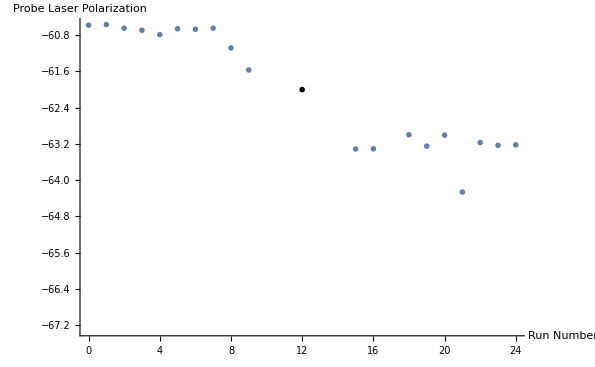

```mathematica
ListPlot[allDetune,LabelStyle->18,PlotMarkers->{Automatic,Large},AxesLabel->{"Run Number","Probe Laser\nPolarization"},Epilog->{Inset[Style["δ=-1.3GHz                           δ=30.19GHz",14],{12,-62}]}]
```

```mathematica
c/(7949152/10000)-ν0
```

30.1965